```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ϵshift=0.0;
ϵ1expdata=Import["Axialstrainstress.txt","Table"];
ϵ3expdata=Import["Radialstrainstress.txt","Table"];
ϵvolexpdata=Import["Volumetricstrainstress.txt","Table"];

ϵ1expdata[[All,1]]*=1.0/100.0;
ϵ3expdata[[All,1]]*=1.0/100.0;

ϵvolexpdata= ϵ1expdata;
ϵvolexpdata [[All,1]]= 2ϵ3expdata[[All,1]]+ϵ1expdata[[All,1]];
```

```mathematica
dataϵAxial={{0.0015406464139036,5.4993495474641891},{0.0016200121202733,5.8599176023780952},{0.0016992638108400,6.2199679156008649},{0.0017785054263159,6.5799724779178819},{0.0018577461285624,6.9399728931323770},{0.0019369867477007,7.2999729309385089},{0.0020162273592718,7.6599729343810452},{0.0020954679701539,8.0199729346945094},{0.0021747085809732,8.3799729347230389},{0.0022539491917868,8.7399729347256514},{0.0023331898025999,9.0999729347258889},{0.0024124304134129,9.4599729347259096},{0.0024916710242260,9.8199729347259161},{0.0025709116350390,10.1799729347259049},{0.0026501522458521,10.5399729347259274},{0.0027293928566651,10.8999729347259162},{0.0028086334674782,11.2599729347259068},{0.0028878740782912,11.6199729347259080},{0.0029671146891042,11.9799729347259039},{0.0030463552999173,12.3399729347259122},{0.0031255959107303,12.6999729347259027},{0.0032048365215434,13.0599729347259323},{0.0032840771323564,13.4199729347259229},{0.0033633177431694,13.7799729347259010},{0.0034425583539825,14.1399729347259164},{0.0035217989647955,14.4999729347259034},{0.0036458512968986,14.8599703005002350},{0.0038363319377530,15.2199662229438868},{0.0040274003869503,15.5799659238054513},{0.0042190225984774,15.9399659578604371},{0.0044111684177130,16.2999660202240833},{0.0046038098837285,16.6599660833185297},{0.0047969209279655,17.0199661447024191},{0.0049904772103562,17.3799662042198335},{0.0051844559807236,17.7399662619205998},{0.0053788359539131,18.0999663178708730},{0.0055735971964062,18.4599663721358276},{0.0057687210231490,18.8199664247783112},{0.0059641899035470,19.1799664758586488},{0.0061599873756978,19.5399665254347106},{0.0063560979679854,19.8999665733274291},{0.0065525071276788,20.2599666201476687},{0.0067492011548793,20.6199666656267375},{0.0069461671426776,20.9799667098138549},{0.0071433929218502,21.3399667527562116},{0.0073408670101229,21.6999667944991721},{0.0075385785653875,22.0599668347395088},{0.0077365173431576,22.4199668741015543},{0.0079346736563555,22.7799669123846371},{0.0081330383391383,23.1399669496269347},{0.0083316027130557,23.4999669858648517}};
dataϵRadial={{0.0000275498136507,5.4993495474641891},{0.0000077084722209,5.8599176023780952},{-0.0000121044428302,6.2199679156008649},{-0.0000319148460469,6.5799724779178819},{-0.0000517250215498,6.9399728931323770},{-0.0000715351763290,7.2999729309385089},{-0.0000913453292213,7.6599729343810452},{-0.0001111554819417,8.0199729346945094},{-0.0001309656346466,8.3799729347230389},{-0.0001507757873500,8.7399729347256514},{-0.0001705859400532,9.0999729347258889},{-0.0001903960927565,9.4599729347259096},{-0.0002102062454598,9.8199729347259161},{-0.0002300163981630,10.1799729347259049},{-0.0002498265508663,10.5399729347259274},{-0.0002696367035695,10.8999729347259162},{-0.0002894468562728,11.2599729347259068},{-0.0003092570089761,11.6199729347259080},{-0.0003290671616793,11.9799729347259039},{-0.0003488773143826,12.3399729347259122},{-0.0003686874670858,12.6999729347259027},{-0.0003884976197891,13.0599729347259323},{-0.0004083077724924,13.4199729347259229},{-0.0004281179251956,13.7799729347259010},{-0.0004479280778989,14.1399729347259164},{-0.0004677382306021,14.4999729347259034},{-0.0004915321502617,14.8599703005002350},{-0.0005221222133697,15.2199662229438868},{-0.0005539899365477,15.5799659238054513},{-0.0005870810635886,15.9399659578604371},{-0.0006213446275248,16.2999660202240833},{-0.0006567325068377,16.6599660833185297},{-0.0006931992102597,17.0199661447024191},{-0.0007307016967101,17.3799662042198335},{-0.0007691992113474,17.7399662619205998},{-0.0008086531347662,18.0999663178708730},{-0.0008490268440063,18.4599663721358276},{-0.0008902855842992,18.8199664247783112},{-0.0009323963505989,19.1799664758586488},{-0.0009753277780378,19.5399665254347106},{-0.0010190500404914,19.8999665733274291},{-0.0010635347568352,20.2599666201476687},{-0.0011087549035197,20.6199666656267375},{-0.0011546847339284,20.9799667098138549},{-0.0012012997031929,21.3399667527562116},{-0.0012485763983302,21.6999667944991721},{-0.0012964924731549,22.0599668347395088},{-0.0013450265879470,22.4199668741015543},{-0.0013941583526592,22.7799669123846371},{-0.0014438682744192,23.1399669496269347},{-0.0014941377082831,23.4999669858648517}};
```

```mathematica
dataϵVolumetric = dataϵRadial;
dataϵVolumetric[[All,1]]=(dataϵAxial[[All,1]]+2 dataϵRadial[[All,1]]);
dataϵAxial[[All,1]]+=0.0004;
dataϵRadial[[All,1]]-=0.0001;

dataϵVolumetric = dataϵRadial;
dataϵVolumetric[[All,1]]=(dataϵAxial[[All,1]]+2 dataϵRadial[[All,1]]);
dataϵVolumetric[[All,1]]-=0.00005;
```

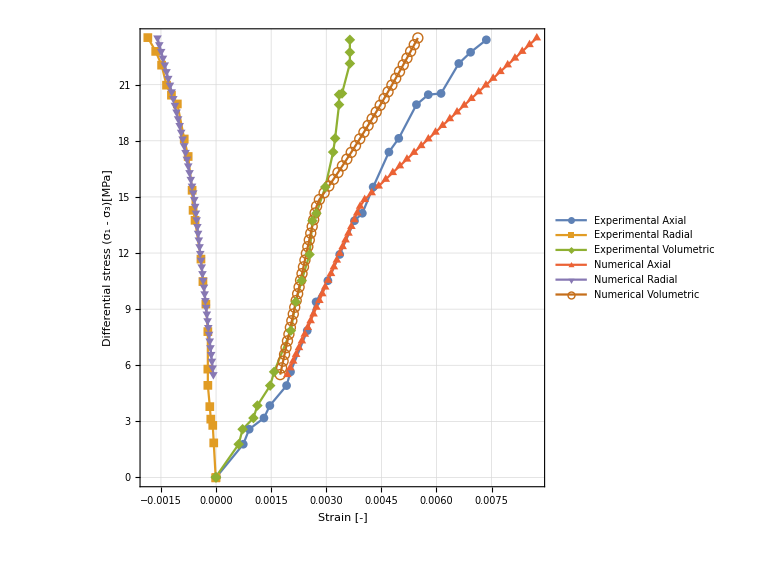

```mathematica
fontsize=18;
Deformationplot=ListPlot[{ϵ1expdata,ϵ3expdata,ϵvolexpdata,dataϵAxial,dataϵRadial,dataϵVolumetric},Joined->True,AspectRatio->1, PlotMarkers->Automatic,PlotRange->All,PlotLegends->{Style["Experimental Axial",fontsize],Style["Experimental Radial",fontsize],Style["Experimental Volumetric",fontsize],Style["Numerical Axial",fontsize],Style["Numerical Radial",fontsize],Style["Numerical Volumetric",fontsize]},Frame->True,GridLines->Automatic, ImageSize->Large,FrameStyle->Directive[Black,fontsize],FrameLabel->{Style["Strain [-]",Black,fontsize],Style["Differential stress (σ_1 - σ_3)[MPa]",Black,fontsize]}]
```

```mathematica
Export["ElasticVerification.png",Deformationplot,ImageResolution->200];
```

## Obtaining Elastic parameters

```mathematica
model=a x +b;
fit=FindFit[ϵ1expdata[[6;;-10]],model,{a,b},x]
λ[Ey_,ν_]=(Ey ν)/((1+ν)(1-2ν));
μ[Ey_,ν_]=Ey/(2(1+ν));
```

{a→4382.87,b→-2.96064}

```mathematica
a
```

a

```mathematica
λ[Ey_,0.2]
```

0.277778 Ey_

## Obtaining Plastic Drucker-Prager G1:: y = 0.7463x + 12.782 R.b2 = 0.59314 G2:: y = 0.5946x + 14.035 R.b2 = 0.41776

```mathematica
adjust={α->0.5946,β->14.035};
eq1=α==Tan[45 + ϕ/2]^2//.adjust;
eq2=β==2c Tan[45 + ϕ/2]//.adjust;
sol=Solve[eq1&& eq2,{ϕ,c}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-91.3137,c→-9.1006},{ϕ→-88.6863,c→9.1006}}

```mathematica
{eq1,eq2}//.sol[[1]]
{eq1,eq2}//.sol[[2]]
```

{True,True}

{True,True}